# Fast Na^+ Current

## Parameters

```mathematica
(*parameters*)
naParameters={gna->2300,ena->50,km->10000,kh->500,vam->-6,vbm->-34,vah->-39,vbh->-40,sam->-20,sbm->-13,sah->-8,sbh->-5,cam->0.11,cbm->15,cah->0.08,cm->1700(*unit conversion*)};
```

## Steady State Equations

```mathematica
(*equations*)

(*steady states: activation*)
minfinite[V_]:=am[V]/(am[V]+bm[V])/.naParameters;
am[V_]:=cam(V-vam)/(1-Exp[(V-vam)/sam])/.naParameters;
bm[V_]:=cbm Exp[(V-vbm)/sbm]/.naParameters;

(*steady states: inactivation*)
hinfinite[V_]:=ah[V]/(ah[V]+bh[V])/.naParameters;
ah[V_]:=cah Exp[(V-vah)/sah]/.naParameters;
bh[V_]:=1/(1+Exp[(V-vbh)/sbh])/.naParameters;
```

```mathematica
(*note the kh equation in the text, as well*)
kh[V_]:=ah[V]+bh[V]
```

```mathematica
kh[-40]
```

0.590652

## Initial Activations and Inactivations

```mathematica
(*find initial activation at holding voltage, -40mV*)initialActivation=NDSolve[{m'[t]==(minfinite[-40]-m[t])*(am[-40]+bm[-40]),m[0]==0}/.naParameters,m[t],{t,0,100000}];
```

```mathematica
m[t]/.initialActivation[[1,All]]/.t->100000
```

0.0339353

```mathematica
initialInactivation=NDSolve[{h'[t]==(hinfinite[-40]-h[t])*(ah[-40]+bh[-40]),h[0]==0}/.naParameters,h[t],{t,0,100000}];
```

```mathematica
h[t]/.initialInactivation[[1,All]]/.t->100000
```

0.153478

## Differential Equation and Plot, just for fun

```mathematica
naCurrentEqs=NDSolve[{cm*V'[t]==-(gna*m[t]^3*h[t]*(V[t]-ena)),h'[t]==(hinfinite[V[t]]-h[t])*(ah[V[t]]+bh[V[t]]),h[0]==0.153478,m'[t]==(minfinite[V[t]]-m[t])*(am[V[t]]+bm[V[t]]),m[0]==0.0339353,V[0]==0}/.naParameters,{V[t],m[t],h[t]},{t,0,0.4}];
```

ReplaceAll::reps: {naParameters} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::deqn: Equation or list of equations expected instead of «1» in the first argument «1».

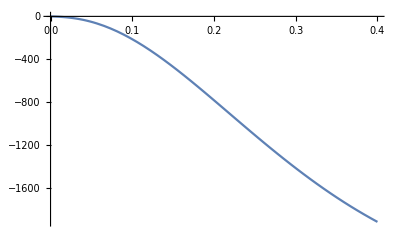

```mathematica
(*plot created to confirm behavior. Not part of the results or replication.*)naCurrentPlot=Plot[Evaluate[gna*m[t]^3*h[t]*(V[t]-ena)/.naCurrentEqs[[1,All]]/.naParameters],{t,0,0.4},PlotRange->All]
```